```mathematica
(*Mathematica*)
```

```mathematica
Clear[ϕ,f,m,r,w,v,sc,g]
```

```mathematica
(* quartic polynomials*)
```

```mathematica
(*2nd minimal Pisot, Meyerhoff,6_1 Knot, tetrahedron, Cyclotomic, Bonacci 4, M003(-4,3)hyperbolic 3 manifold,8_18 Knot,8_21 Knot,M015(81) hyperbolic manifold,m011 cusped Manifold,m079 cusped manifold,m026 cusped manifold,cyclic,Miniamal Pisot, second cubic pisot, cyclic3,,reverse cyclic3,Weeks Hyperbolic manifold,Bonacci 3,2nd Bonacci,Jones X1,Jones X4*)
```

```mathematica
p={x^4-x^3-1,x^4-x-1,x^4+x^2-x+1,x^4-2*I*Sqrt[3]*x^2+1,x^4+x^3+x^2+x+1,x^4-x^3-x^2-x-1,x^4-x^3+x^2+x-1,x^4-2*x^3+x^2-2*x+1,x^4-x^3+x+1,x^4-x^2-3*x-2,x^4-2*x^3+x^2-x-1,x^4-x^3+4*x^2-3*x+2,x^4-x^3+x^2-x-1,x^4-1,(x+1)*(x^3-x-1),(x+1)*(x^3-x^2-1),(x+1)(x^3-1),(x-1)*(x^3+1),(x^3-x^2+1)*(x-1),(x+1)*(x^3-x^2-x-1),(x-1)*(x^3-x^2-x-1),(x+1)*(x^3-x-2),x^4-2*x^3-x^2+2*x-1}
```

{-1-x^3+x^4,-1-x+x^4,1-x+x^2+x^4,1-2 ⅈ √3 x^2+x^4,1+x+x^2+x^3+x^4,-1-x-x^2-x^3+x^4,-1+x+x^2-x^3+x^4,1-2 x+x^2-2 x^3+x^4,1+x-x^3+x^4,-2-3 x-x^2+x^4,-1-x+x^2-2 x^3+x^4,2-3 x+4 x^2-x^3+x^4,-1-x+x^2-x^3+x^4,-1+x^4,(1+x) (-1-x+x^3),(1+x) (-1-x^2+x^3),(1+x) (-1+x^3),(-1+x) (1+x^3),(-1+x) (1-x^2+x^3),(1+x) (-1-x-x^2+x^3),(-1+x) (-1-x-x^2+x^3),(1+x) (-2-x+x^3),-1+2 x-x^2-2 x^3+x^4}

```mathematica
ϕ=N[GoldenRatio]
```

1.61803

```mathematica
Exp[2*π*I*ϕ]
```

-0.737369-0.67549 ⅈ

```mathematica
CompanionMatrix[p_, x_] := Module[{cl=CoefficientList[p, x], deg, m}, cl=Drop[cl/Last[cl], -1]; deg=Length[cl]; If[deg==1, {-cl}, m=RotateLeft[IdentityMatrix[deg]]; m[[ -1]]=-cl; Transpose[m]]];
```

```mathematica
m=Transpose[CompanionMatrix[p[[1]],x]]
```

{{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,0,0,1}}

```mathematica
N[Eigenvalues[m]]
```

{1.38028,0.219447+0.914474 ⅈ,0.219447-0.914474 ⅈ,-0.819173}

```mathematica
r[i_]:=x/.NSolve[p[[1]]==0,x][[i]]
```

```mathematica
v=Table[r[i],{i,4}]
```

{-0.819173,0.219447-0.914474 ⅈ,0.219447+0.914474 ⅈ,1.38028}

```mathematica
Abs[%]
```

{0.819173,0.940436,0.940436,1.38028}

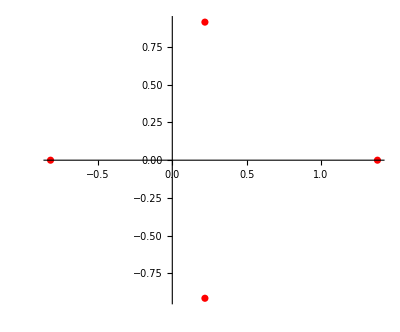

```mathematica
ComplexListPlot[v,PlotStyle->Red]
```

```mathematica
sc=2.0;
```

```mathematica
w={{{Re[r[1]],Im[r[1]]},{Re[r[2]],Im[r[2]]}},{{Re[r[1]],Im[r[1]]},{Re[r[3]],Im[r[3]]}},{{Re[r[1]],Im[r[1]]},{Re[r[2]],Im[r[2]]}},{{Re[r[2]],Im[r[2]]},{Re[r[3]],Im[r[3]]}},{{Re[r[2]],Im[r[2]]},{Re[r[4]],Im[r[4]]}},{{Re[r[3]],Im[r[3]]},{Re[r[4]],Im[r[4]]}}}
```

{{{-0.819173,0},{0.219447,-0.914474}},{{-0.819173,0},{0.219447,0.914474}},{{-0.819173,0},{0.219447,-0.914474}},{{0.219447,-0.914474},{0.219447,0.914474}},{{0.219447,-0.914474},{1.38028,0}},{{0.219447,0.914474},{1.38028,0}}}

```mathematica
Table[Eigenvalues[w[[i]]]//Chop,{i,6}]
```

{{-0.914474,-0.819173},{0.914474,-0.819173},{-0.914474,-0.819173},{0.566961+0.28269 ⅈ,0.566961-0.28269 ⅈ},{0.109724+1.11812 ⅈ,0.109724-1.11812 ⅈ},{1.23856,-1.01911}}

```mathematica
(* Projecting the  2nd Minimal Pisot Polynomial onto a qz^(2*n) Hermann rings Julia*)
```

```mathematica
f[z_,1]=Exp[2*π*I*ϕ]*z^2*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1));
f[z_,2]=Exp[2*π*I*ϕ]*z^4*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1));
f[z_,3]=Exp[2*π*I*ϕ]*z^6*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1));
f[z_,4]=Exp[2*π*I*ϕ]*z^8*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1));
f[z_,5]=Exp[2*π*I*ϕ]*z^10*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1));
f[z_,6]=Exp[2*π*I*ϕ]*z^12*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1));
```

```mathematica
g=Table[JuliaSetPlot[f[z,i],z, Method -> "OrbitDetection",ColorFunction->Hue,ImageSize->2000,PlotStyle->{Opacity[0.2],Red,PointSize[0.0005]},AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality","Bound"->12,Frame->False,PlotRange->All],{i,6}];
```

```mathematica
Export["Julia_4root_2ndminimalpisot_Polynomial_z2n_Herman_rings_Hue_scale2.jpg",GraphicsGrid[{{g[[1]],g[[2]],g[[3]]},{g[[4]],g[[5]],g[[6]]}},ImageSize->{6000,4000}]]
```

Julia_4root_2ndminimalpisot_Polynomial_z2n_Herman_rings_Hue_scale2.jpg

```mathematica
(*end*)
```